## Kepler Problem (Inverse Square Law)

```mathematica
(*Using Automatic method*)
```

```mathematica
eqns={x'[t]==px[t],y'[t]==py[t],px'[t]==(-x[t])/((x[t]^2+y[t]^2)^(3/2)),py'[t]==(-y[t])/((x[t]^2+y[t]^2)^(3/2))};
```

```mathematica
ics={x[0]==0.4,y[0]==0,px[0]==0,py[0]==2};
```

```mathematica
vars={x,y,px,py};
```

```mathematica
sol=NDSolve[{eqns,ics},vars,{t,0,100}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],px→InterpolatingFunction[…],py→InterpolatingFunction[…]}}

```mathematica
xp=x/.sol[[1]];
```

```mathematica
yp=y/.sol[[1]];
```

```mathematica
pxp=px/.sol[[1]];
```

```mathematica
pyp=py/.sol[[1]];
```

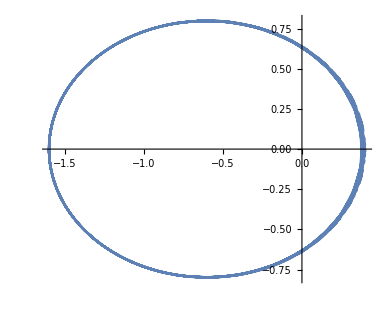

```mathematica
ParametricPlot[{xp[t],yp[t]},{t,0,100},PlotPoints->10]
```

```mathematica
(*Total energy*)
```

```mathematica
H[t_]=1/2(pxp[t]^2+pyp[t]^2)-1/(√(xp[t]^2+yp[t]^2));
```

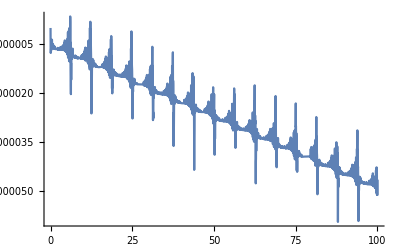

```mathematica
Plot[H[t],{t,0,100}]
```

```mathematica
(*Total angular momentum*)
```

```mathematica
L[t_]=xp[t]pyp[t]-yp[t]pxp[t];
```

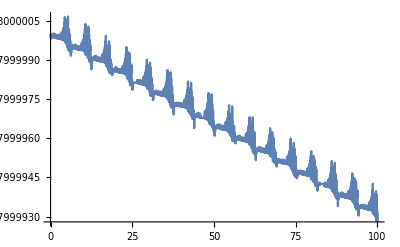

```mathematica
Plot[L[t],{t,0,100}]
```

```mathematica
(*Explicit Euler*)
```

```mathematica
solee=NDSolve[{eqns,ics},vars,{t,0,100},Method->"ExplicitEuler",StartingStepSize->0.05,MaxSteps->Infinity];
```

```mathematica
xe=x/.solee[[1]];
```

```mathematica
ye=y/.solee[[1]];
```

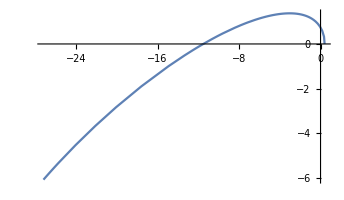

```mathematica
ParametricPlot[{xe[t],ye[t]},{t,0,100},PlotPoints->10]
```

```mathematica
pxe=px/.solee[[1]];
```

```mathematica
pye=py/.solee[[1]];
```

```mathematica
(*Total energy*)
```

```mathematica
He[t_]=1/2(pxe[t]^2+pye[t]^2)-1/(√(xe[t]^2+ye[t]^2));
```

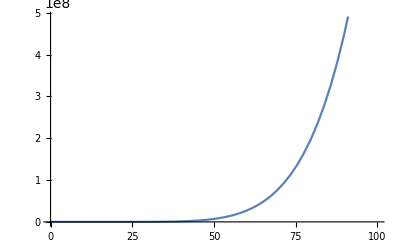

```mathematica
Plot[He[t],{t,0,100}]
```

```mathematica
(*Total angular momentum*)
```

```mathematica
Le[t_]=xe[t]pye[t]-ye[t]pxe[t];
```

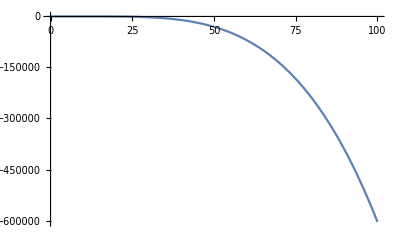

```mathematica
Plot[Le[t],{t,0,100}]
```

```mathematica
(*Simplectic Method:symplectic partitioned Runge–Kutta method*)
```

```mathematica
sols=NDSolve[{eqns,ics},vars,{t,0,10},Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->3,"PositionVariables"->{x[t],y[t]}},StartingStepSize->0.05,MaxSteps->Infinity];
```

```mathematica
xs=x/.sols[[1]];
```

```mathematica
ys=y/.sols[[1]];
```

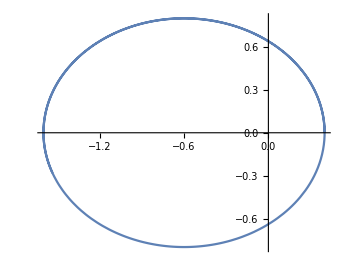

```mathematica
ParametricPlot[{xs[t],ys[t]},{t,0,10},PlotPoints->10]
```

```mathematica
pxs=px/.sols[[1]];
```

```mathematica
pys=py/.sols[[1]];
```

```mathematica
(*Total energy*)
```

```mathematica
Hs[t_]=1/2(pxs[t]^2+pys[t]^2)-1/(√(xs[t]^2+ys[t]^2));
```

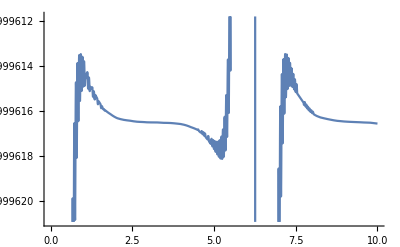

```mathematica
Plot[Hs[t],{t,0,10}]
```

```mathematica
(*Total angular momentum*)
```

```mathematica
Ls[t_]=xs[t]pys[t]-ys[t]pxs[t];
```

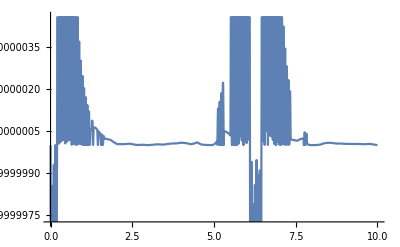

```mathematica
Plot[Ls[t],{t,0,10}]
```

## Simple Harmonic Oscillator

```mathematica
(*Using Automatic method*)
```

```mathematica
eqns={p'[t]==-q[t],q'[t]==p[t]};
```

```mathematica
vars={p,q};
```

```mathematica
ics={q[0]==1,p[0]==0}
```

{q[0]==1,p[0]==0}

```mathematica
sol=NDSolve[{eqns,ics},vars,{t,0,100}]
```

{{p→InterpolatingFunction[…],q→InterpolatingFunction[…]}}

```mathematica
pp=p/.sol[[1]]
```

InterpolatingFunction[…]

```mathematica
qq=q/.sol[[1]]
```

InterpolatingFunction[…]

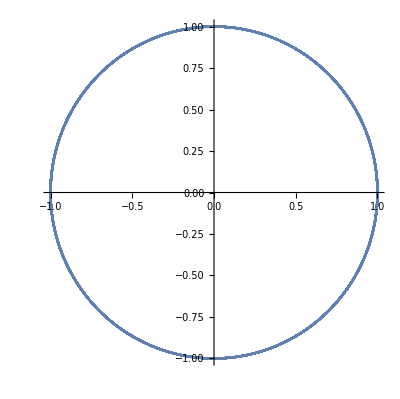

```mathematica
ParametricPlot[{qq[t],pp[t]},{t,0,100},PlotPoints->100]
```

```mathematica
H[t_]=pp[t]^2/2+qq[t]^2/2
```

1/2 (InterpolatingFunction[…][t])^2+1/2 (InterpolatingFunction[…][t])^2

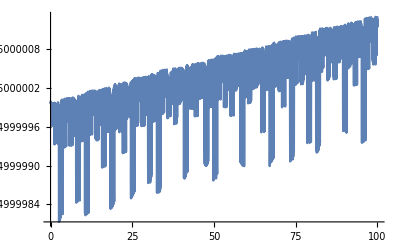

```mathematica
Plot[H[t],{t,0,100}]
```

```mathematica
(*Using Explicit Euler method*)
```

```mathematica
solee=NDSolve[{eqns,ics},vars,{t,0,100},Method->"ExplicitEuler",StartingStepSize->0.05,MaxSteps->Infinity];
```

```mathematica
ppe=p/.solee[[1]];
```

```mathematica
qqe=q/.solee[[1]];
```

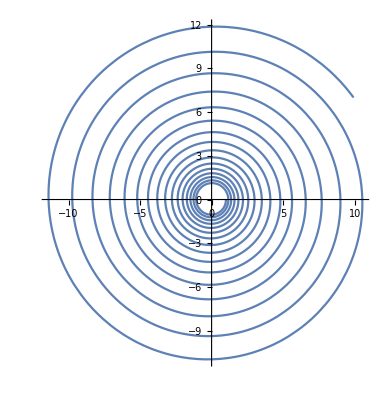

```mathematica
ParametricPlot[{qqe[t],ppe[t]},{t,0,100},PlotPoints->100]
```

```mathematica
He[t_]=ppe[t]^2/2+qqe[t]^2/2;
```

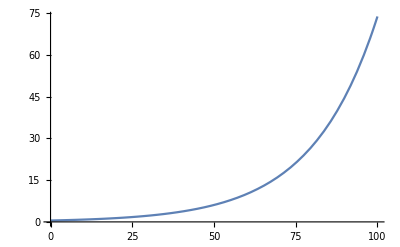

```mathematica
Plot[He[t],{t,0,100}]
```

```mathematica
(*Simplectic Method:symplectic partitioned Runge–Kutta method*)
```

```mathematica
sols=NDSolve[{eqns,ics},vars,{t,0,100},Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->2,"PositionVariables"->{q[t]}},StartingStepSize->0.05,MaxSteps->Infinity];
```

```mathematica
pps=p/.sols[[1]];
```

```mathematica
qqs=q/.sols[[1]];
```

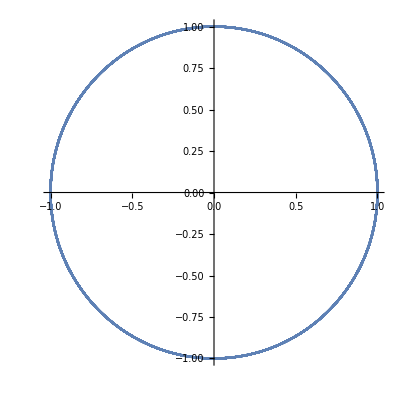

```mathematica
ParametricPlot[{qqs[t],pps[t]},{t,0,100},PlotPoints->100]
```

```mathematica
Hs[t_]=pps[t]^2/2+qqs[t]^2/2;
```

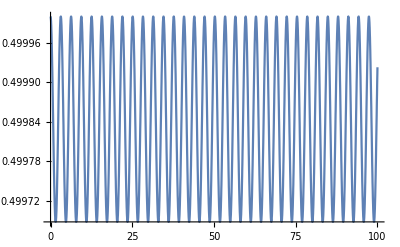

```mathematica
Plot[Hs[t],{t,0,100}]
```

Symplectic method produces the correct solutions with minimal of error in the energy value. For solving ode/pde with a conserved quantities, one has to use Symplectic integrators/ methods.